# Homework 22

## Problem 22.1

A system of two objects in otherwise empty space has a reduced mass of 100 kg. At time t=0, the objects are separated by 10 meters and the radial velocity of each object is zero. They experience an attractive potential of magnitude alpha / r. As discussed in class, the relative position between the two objects can be represented by a fictitious particle. The initial momentum (in the cm frame) of this fictitious particle is p0=2500 kg m/s. We wish to determine the behavior of this system as a function of time.

We'll call the coordinates r and phi.

```mathematica
Clear["`*"];
```

First, set the numerical values. (Note the potential is really big compared to gravity!)

```mathematica
mu=100;
p0=2500;
r0=10;
alpha=.1875*10^7;
```

Find the potential energy and the force.

```mathematica
U=-alpha/r;
Fr=-D[U,r];
```

### Solutions

```mathematica
U$=-alpha/r;
Fr$=-D[U,r];
If[FullSimplify[Solve[U==U$,r]]=={{}},Print["U is correct."],Print["U is incorrect"]];
If[FullSimplify[Solve[U==-U$,r]]=={{}},Print["An attractive potential is negative."]];
If[FullSimplify[Solve[Fr==Fr$,r]]=={{}},Print["Fr is correct."],Print["Fr is incorrect"]]
If[FullSimplify[Solve[Fr==-Fr$,r]]=={{}},Print["Remember Fr=-dU/dr"]]
```

U is correct.

Fr is correct.

Find the angular momentum L and the total energy Et based on the initial conditions. Note that you can apply the usual formulas for angular momentum and kinetic energy (as expressed in terms of momentum) to our fictitious particle with reduced mass μ.

Find the centrifugal potential Ucent as a function of r.

```mathematica
L=p0*r0;
Et=p0^2/(2*mu)-alpha/r0;
Ucent=L^2/(2*mu*r^2);
```

### Solutions

```mathematica
L$=p0*r0;
Et$=p0^2/2/mu-alpha/r0;
Ucent$=L^2/2/mu/r^2;
If[FullSimplify[Solve[L==L$,xx]]=={{}},Print["L is correct."],Print["L is incorrect"]]
If[FullSimplify[Solve[Et==Et$,xx]]=={{}},Print["Et is correct."],Print["Et is incorrect"]]
If[FullSimplify[Solve[Et==p0^2/2/mu,r]]=={{}},
Print["You left out the potential energy."]]
If[FullSimplify[Solve[Et==-alpha/a,r]]=={{}},
Print["You left out the kinetic energy."]]
If[FullSimplify[Solve[Ucent==Ucent$,r]]=={{}},Print["Ucent is correct."],Print["Ucent is incorrect"]]
If[FullSimplify[Solve[Ucent==L^2/mu/r^3,r]]=={{}},
Print["You put the centrifugal force rather than the centrifugal potential."]]
```

L is correct.

Et is correct.

Ucent is correct.

Now let’s plot these results on a couple of scales.

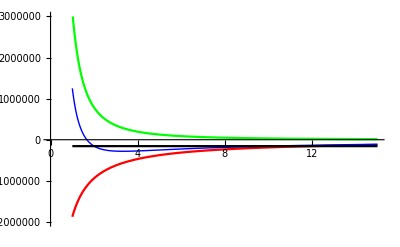

```mathematica
Plot[{U,Ucent,U+Ucent,Et},{r,1,15},PlotStyle->{Red,Green,{Blue,Thick},Black},PlotRange->{-2*10^6,3*10^6}]
```

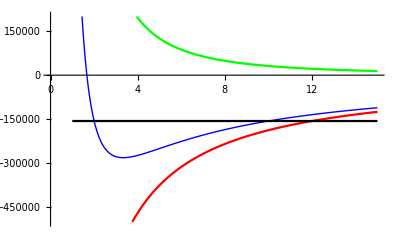

```mathematica
Plot[{U,Ucent,U+Ucent,Et},{r,1,15},PlotStyle->{Red,Green,{Blue,Thick},Black},PlotRange->{-5*10^5,2*10^5}]
```

Can you estimate the turning points of the motion?

Write the radial and angular equations of motion and solve them subject to the boundary conditions outlined above. Be sure to include the explicit time dependence.
Hint : The phi equation comes from the expression for L, which is a constant of the motion.

```mathematica
req=mu*r''[t]==(Fr/.r->r[t])+L^2/(mu*r[t]^3);
phieq=phi'[t]==L/(mu*r[t]^2);
```

### Solutions

```mathematica
req$=mu*r''[t]==(Fr/.r->r[t])+L^2/mu/r[t]^3;
phieq$=phi'[t]==L/(mu*r[t]^2);
If[FullSimplify[Solve[req==req$,r[t]]]=={{}},Print["req is correct."],Print["req is incorrect."]]
If[FullSimplify[Solve[phieq==phieq$,r[t]]]=={{}},Print["phieq is correct."],Print["phieq is incorrect."]]
```

req is correct.

phieq is correct.

Now solve the equation.

```mathematica
sol1=NDSolve[{req,phieq,r[0]==r0,r'[0]==0,phi[0]==0},{r,phi},{t,0,3}]
```

{{r→InterpolatingFunction[…],phi→InterpolatingFunction[…]}}

Let’s generate some plots.

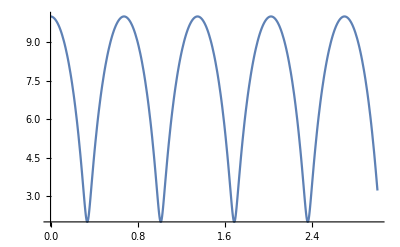

```mathematica
Plot[r[t]/.sol1,{t,0,3}]
```

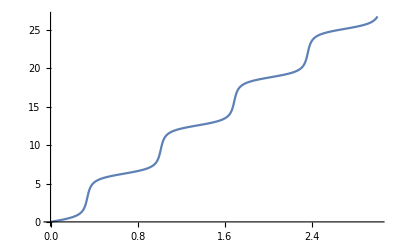

```mathematica
Plot[phi[t]/.sol1,{t,0,3}]
```

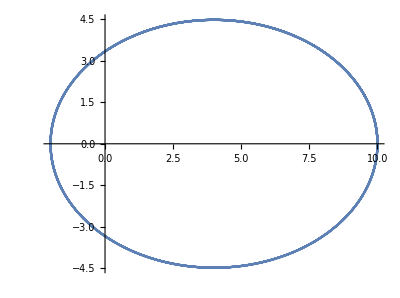

```mathematica
ParametricPlot[{r[t]*Cos[phi[t]],r[t]*Sin[phi[t]]}/.sol1,{t,0,3}]
```

Inspect the parametric plot above and ensure that the turning points (i.e. rmin and rmax) agree with what you predicted previously.

Now we’ll see how the various energy terms vary with r.
Write expressions for the following as functions of r[t] and r’[t] :
TKE transverse (phi direction) kinetic energy
RKE radial (r direction) kinetic energy
PE the potential energy
CP the centrifugal potential
Ueff the effective potential-- the sum of the last two.
Etot the total energy of the system.

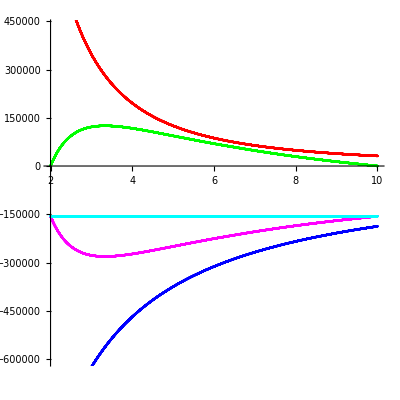

```mathematica
TKE=L^2/(2*mu*r[t]^2);
RKE=mu/2*r'[t]^2;
PE=-alpha/r[t];
CP= L^2/(2*mu*r[t]^2);
Ueff=PE+CP;
Etot=TKE+RKE+PE;
ParametricPlot[{{r[t],TKE}/.sol1,{r[t],RKE}/.sol1,{r[t],PE}/.sol1,{r[t],Ueff}/.sol1,{r[t],Etot}/.sol1},{t,0,3},AspectRatio->1,PlotStyle->{Red,Green,Blue,Magenta,Cyan}]
```

### Solutions

```mathematica
TKE$ = L^2/2/mu/r[t]^2;
RKE$ = mu/2*r'[t]^2;
PE$= -alpha/r[t];
CP$= L^2/2/mu/r[t]^2;
Ueff$ = PE$ + CP$;
Etot$ = TKE$ + RKE$ + PE$;
If[FullSimplify[Solve[TKE==TKE$],r]=={{}},Print["TKE is correct."],Print["TKE is incorrect"]]
If[FullSimplify[Solve[RKE==RKE$],r]=={{}},Print["RKE is correct."],Print["RKE is incorrect"]]
If[FullSimplify[Solve[PE==PE$],r]=={{}},Print["PE is correct."],Print["PE is incorrect"]]
If[FullSimplify[Solve[CP==CP$],r]=={{}},Print["CP is correct."],Print["CP is incorrect"]]
If[FullSimplify[Solve[Ueff==Ueff$],r]=={{}},Print["Ueff is correct."],Print["Ueff is incorrect"]]
If[FullSimplify[Solve[Etot==Etot$],r]=={{}},Print["Etot is correct."],Print["Etot is incorrect"]]
```

TKE is correct.

RKE is correct.

PE is correct.

CP is correct.

Ueff is correct.

Etot is correct.

## Problem 22.2

Redo the problem, but let the magnitude of the potential be alpha / r^1.05 rather than alpha / r. You will notice that the orbit does not close in on itself (i.e. it is not periodic). This illustrates the fact that having a 1/r potential (or equivalently 1/r^2 force) is a very special situation that allows for periodic orbits.

Copy and paste the cells above and modify the inputs to account for the 1.05 power. You do not need to change very much! Don’t worry about trying to check your work with the solution cells (they won’t work with the modified potential energy).

For a pretty picture, solve your differential equations up to a time of t=30 seconds and set the limit of your (x, y) parametric plot to t=30.

```mathematica
Clear["`*"];
```

```mathematica
Quit[]
```

### Hint

Except for solutions, the following expressions are the only ones that need changing.
 U=-alpha/r^1.05
 Et=p0^2/2/mu-alpha/a^1.05
 PE=-alpha/r(t)^1.05

```mathematica
mu=100;
p0=2500;
r0=10;
alpha=.1875*10^7;
```

```mathematica
U=-alpha/r^1.05;
Fr=-D[U,r];
```

```mathematica
L=p0*r0;
Et=p0^2/(2*mu)-alpha/r0^1.05;
Ucent=L^2/(2*mu*r^2);
```

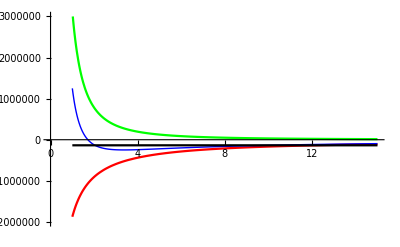

```mathematica
Plot[{U,Ucent,U+Ucent,Et},{r,1,15},PlotStyle->{Red,Green,{Blue,Thick},Black},PlotRange->{-2*10^6,3*10^6}]
```

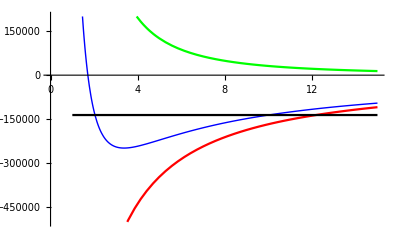

```mathematica
Plot[{U,Ucent,U+Ucent,Et},{r,1,15},PlotStyle->{Red,Green,{Blue,Thick},Black},PlotRange->{-5*10^5,2*10^5}]
```

```mathematica
req=mu*r''[t]==(Fr/.r->r[t])+L^2/(mu*r[t]^3);
phieq=phi'[t]==L/(mu*r[t]^2);
```

```mathematica
sol1=NDSolve[{req,phieq,r[0]==r0,r'[0]==0,phi[0]==0},{r,phi},{t,0,30}]
```

{{r→InterpolatingFunction[…],phi→InterpolatingFunction[…]}}

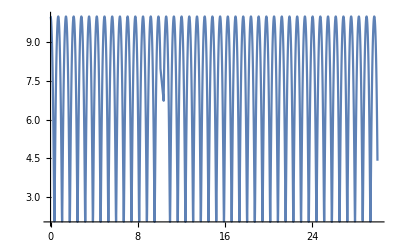

```mathematica
Plot[r[t]/.sol1,{t,0,30}]
```

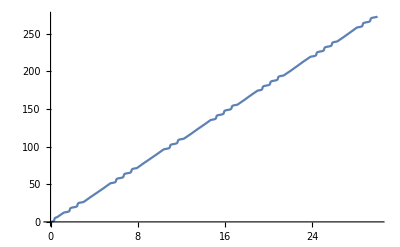

```mathematica
Plot[phi[t]/.sol1,{t,0,30}]
```

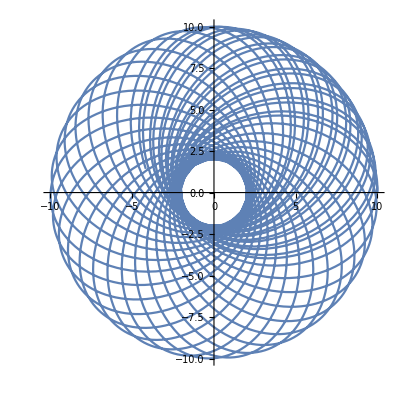

```mathematica
ParametricPlot[{r[t]*Cos[phi[t]],r[t]*Sin[phi[t]]}/.sol1,{t,0,30}]
```

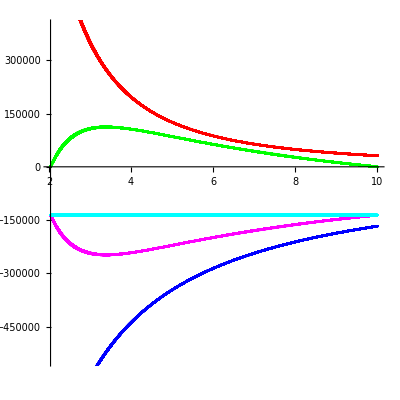

```mathematica
TKE=L^2/(2*mu*r[t]^2);
RKE=mu/2*r'[t]^2;
PE=-alpha/r[t]^1.05;
CP= L^2/(2*mu*r[t]^2);
Ueff=PE+CP;
Etot=TKE+RKE+PE;
ParametricPlot[{{r[t],TKE}/.sol1,{r[t],RKE}/.sol1,{r[t],PE}/.sol1,{r[t],Ueff}/.sol1,{r[t],Etot}/.sol1},{t,0,30},AspectRatio->1,PlotStyle->{Red,Green,Blue,Magenta,Cyan}]
```

## Written Problems

-Graphics-